Equation: 5.78321 x u[x]+u'[x]+x u''[x]==0

Boundary conditions: {u[0]==1,u[1]==0}

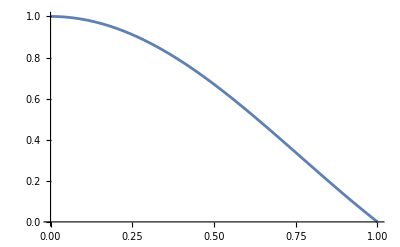

```mathematica
Clear["Global`*"]
d[x_]:=-x;
b[x_]:=0;
c[x_]:=mu^2 x;
f[x_]:=0;

(*d[x_]:=-Sin[x];
b[x_]:=-Cos[x];
c[x_]:=Sin[x];
f[x_]:=1;*)

alpha=0;
beta=1;
mu0=1;
mu1=0;
mu=2.40483;

n=9;
h=(beta-alpha)/(n+1);
eq=-D[(d[x]*u'[x]),x]+b[x]*u'[x]+c[x]*u[x]==f[x];
bc={u[alpha]==mu0,u[beta]==mu1};
Print["Equation: ",eq];
Print["Boundary conditions: ",bc];
ua=Quiet@NDSolveValue[{eq,bc},u,{x,alpha,beta}];
Print[Show[Plot[{ua[x]},{x,alpha,beta}]]]

fea[alpha_,n_,h_]:=Module[{xgrid,As,Ac,Am,fv,A},
xgrid=Table[alpha+h*i,{i,0,n}];
As=Table[0,{i,1,n+1},{j,1,n+1}];
Ac=Table[0,{i,1,n+1},{j,1,n+1}];
Am=Table[0,{i,1,n+1},{j,1,n+1}];
fv=Table[0,{i,1,n+1}];
For[i=2,i<n,i++,
Napp=a0+a1*x;
(*eq3=Napp/.{x->xgrid[[i-1]]};*)
eq1=Napp/.{x->xgrid[[i]]};
eq2=Napp/.{x->xgrid[[i+1]]};
sol=Solve[{eq1==x1,eq2==x2},{a0,a1}];
Napp=Napp/.sol[[1]];
(*N3=Coefficient[Napp,x3];*)
N1=Coefficient[Napp,x1];
N2=Coefficient[Napp,x2];
Ni={{N1,N2}};
(*Print[Ni//MatrixForm];*)
(*Print[(Transpose[Ni].Ni)//MatrixForm];*)
dNi=D[Ni,x];
Ase=Integrate[d[x]*Transpose[dNi].dNi,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[dNi].dNi,{x,xgrid[[i]],xgrid[[i+1]]}](-xgrid[[i]]+xgrid[[i+1]])//MatrixForm];*)
Ace=Integrate[b[x]*Transpose[Ni].dNi,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[Ni].dNi,{x,xgrid[[i]],xgrid[[i+1]]}]*2//MatrixForm];*)
Ame=Integrate[c[x]*Transpose[Ni].Ni,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[Ni].Ni,{x,xgrid[[i]],xgrid[[i+1]]}]*6/(-xgrid[[i]]+xgrid[[i+1]])//MatrixForm];*)
fve=Integrate[f[x]*Transpose[Ni],{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[fve//MatrixForm];*)
Do[
As[[i+j,i+k]]+=Ase[[j+1,k+1]];
Ac[[i+j,i+k]]+=Ace[[j+1,k+1]];
Am[[i+j,i+k]]+=Ame[[j+1,k+1]],
{j,0,1},{k,0,1}];
Do[
fv[[i+j]]+=fve[[j+1,1]],
{j,0,1}];
];
A=(As+Ac+Am);
A[[1,1]]=A[[n+1,n+1]]=1;
fv[[1]]+=mu0;fv[[n+1]]+=mu1;
A[[2,2]]+=d[alpha+h/2]/h+b[alpha+h/2]/2+c[alpha+h/2]/3*h;
A[[n,n]]+=d[beta-h/2]/h-b[beta-h/2]/2+c[beta-h/2]/3*h;
fv[[2]]+=d[alpha+h/2]/h+b[alpha+h/2]/2+c[alpha+h/2]/3*h;
sole=LinearSolve[A,fv];
Return[sole];
]
sole=fea[alpha,n,h]
ErrList={};
Do[
h=(beta-alpha)/(n+1);
sole=fea[alpha,n,h];
xgrid=Table[alpha+h*i,{i,0,n}];
exact=Table[ua[xgrid[[i]]],{i,1,Length[xgrid]}];
AppendTo[ErrList,{n,Max[Abs[exact-sole]]}],
{n,9,100}]
```

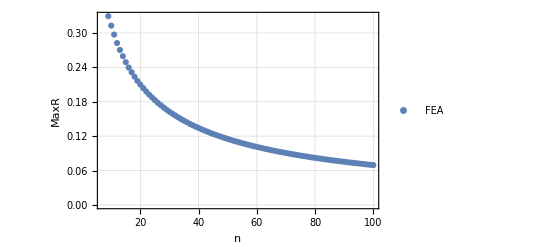

```mathematica
Print[ListPlot[ErrList,FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["n",16,Black,FontFamily->"Cambria"],Style["MaxR",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All,
PlotLegends->Placed[{Style["FEA",16,Black,FontFamily->"Cambria"],Style["DiffScheme2",16,Black,FontFamily->"Cambria"]},Right]]]
```